```mathematica
NormalizeData[symbol_,start_,end_]:=FinancialData[symbol,{start,end}]//Transpose@{#[[All,1]],#[[All,2]]/First@#[[All,2]]}&
PortfolioChart[stocks_,start_,end_]:=Module[{s,portfolio,data,symbols},
s=NormalizeData[#,start,end]&/@stocks;
portfolio=Transpose@{s[[1]][[All,1]],Mean/@Transpose@(#[[All,2]]&/@s)};
data=s~Join~{portfolio};
symbols=stocks~Join~{"portfolio"};
DateListPlot[data,PlotLegends->symbols,PlotTheme->"Detailed",ImageSize->Large,BaseStyle->{FontSize->20},PlotRange->All]
]
```

```mathematica
start=DatePlus[Today,-Quantity[5,"Years"]];
start2=DatePlus[Today,-Quantity[2,"Years"]];
end=Today
```

Tue 1 Nov 2016

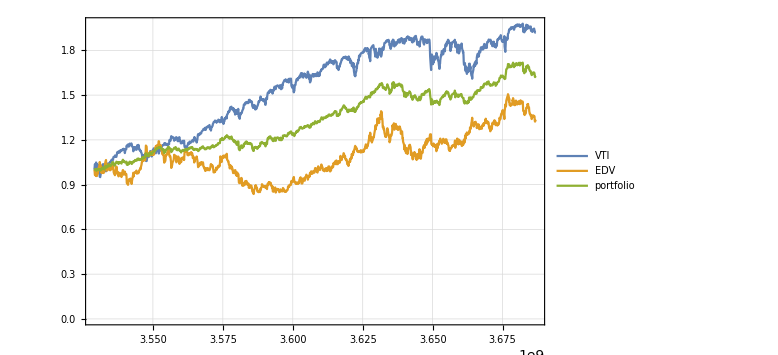

```mathematica
PortfolioChart[{"VTI","EDV"},start,end]
```

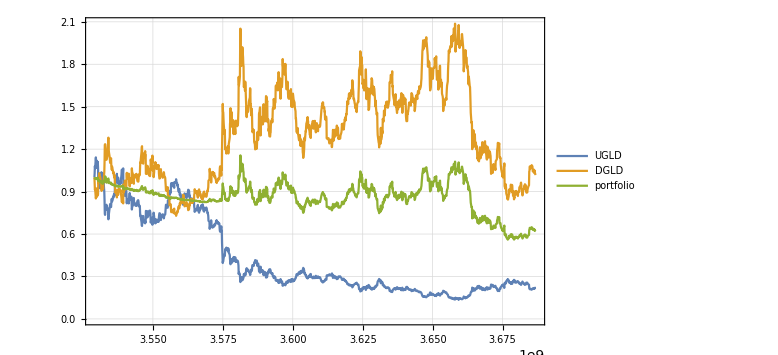

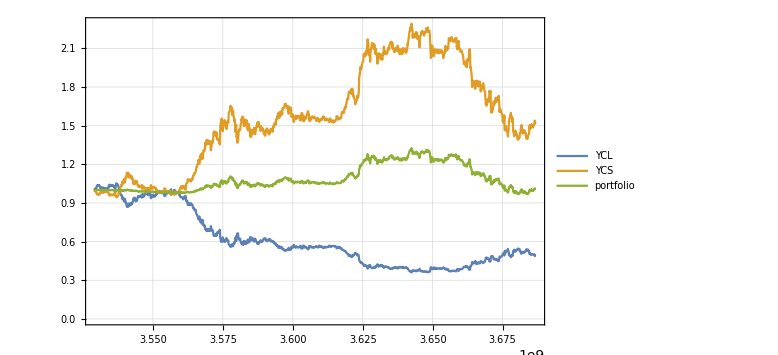

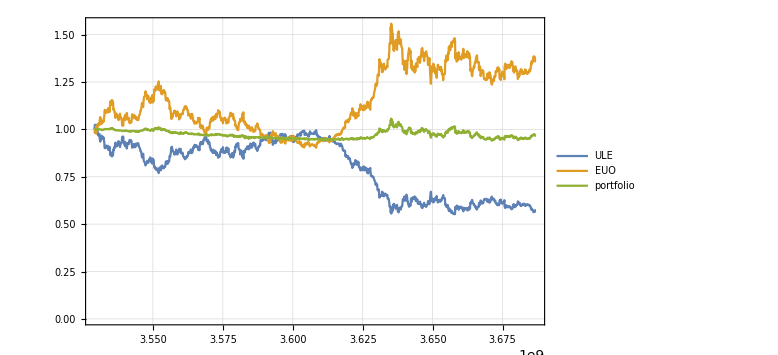

```mathematica
PortfolioChart[{"UGLD","DGLD"},start,end]
PortfolioChart[{"YCL","YCS"},start,end]
PortfolioChart[{"ULE","EUO"},start,end]
```

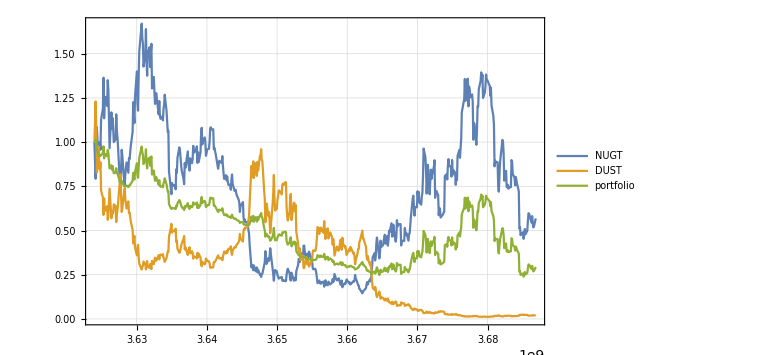

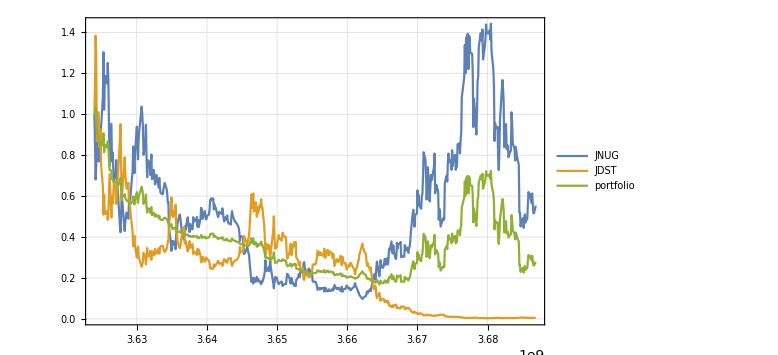

```mathematica
PortfolioChart[{"NUGT","DUST"},start2,end]
PortfolioChart[{"JNUG","JDST"},start2,end]
```

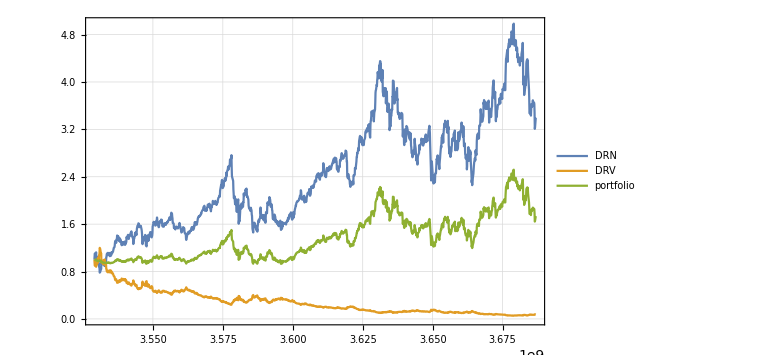

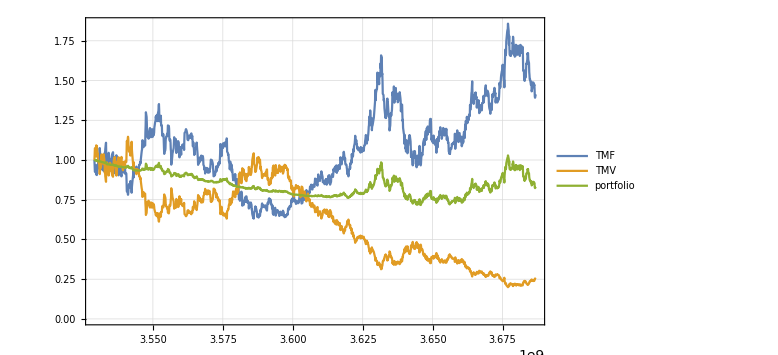

```mathematica
PortfolioChart[{"DRN","DRV"},start,end]
PortfolioChart[{"TMF","TMV"},start,end]
```

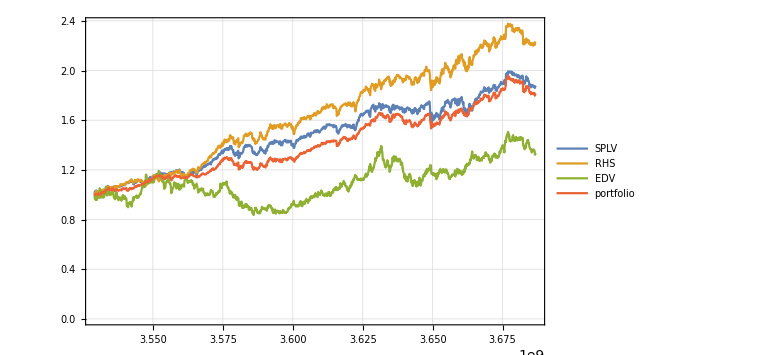

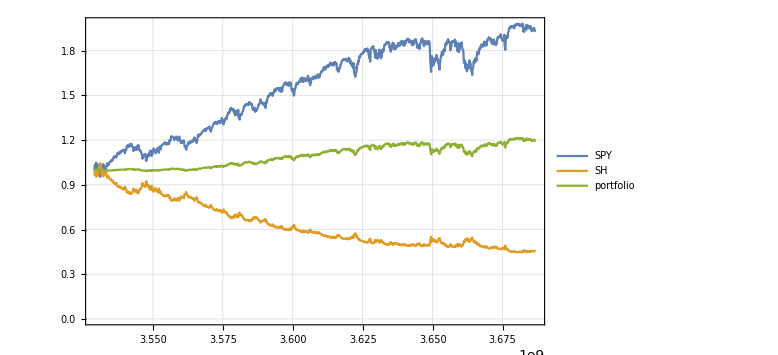

```mathematica
PortfolioChart[{"SPLV","RHS","EDV"},start,end]
PortfolioChart[{"SPY","SH"},start,end]
```